# Post Processing

This notebook is used to extract collapse rate from the raw thermal collapse data. 

Raw data is saved in ParentDirectory[]<>“data/thermal-collapse-data/...” where files are named
 
“topological_charge_during_relaxation(dynamics)_*”
“energy_during_relaxation(dynamics)_*”
“effective_size_during_relaxation(dynamics)_*”
“spin_field_after_relaxation(dynamics)_*”

Modifier ‘relaxation’ refers to data acquired during T=0 initial skyrmion relaxation, while ‘dynamics’ refers to data acquired during thermal collapse computation. Suffixes of filenames are parameter values. 

In order to extract collapse rate and energy barrier, need to process the topological charge data to determine the collapse time for various temperatures and fit the data to an exponential. 

To save time, it is useful to collect collapse times from all data runs and save them to their respective files in the folder “processed-collapse-times”

```mathematica
SetDirectory[NotebookDirectory[]];
macSize = 500;linSize = 1000;
SetOptions[{MatrixPlot,ListVectorPlot},ImageSize->linSize,ImagePadding->{{50,70},{50,50}},LabelStyle->{Directive["Times",14,Black],FontFamily->"Times"}];
SetOptions[{ListPlot,ListLogPlot,ListLogLogPlot,Plot,LogPlot,LogLogPlot,Histogram},Frame->True,AspectRatio->1/GoldenRatio,ImageSize->linSize,LabelStyle->{Directive["Times",18,Black],FontFamily->"Times",ImagePadding->{{100,100},{100,100}}}];
```

Functions

```mathematica
(* 

Input: dirPrefix = directory where data is stored, T = temperature,
H = external field, DMI = Dzyaloshinskii-Moraya Interaction, tfree =
free evolution time from thermal collapse script. ;

	Sample inputs: 
dirPrefix = ParentDirectory[]<>"/data/t-collapse-data", 
T = 0.1, H = -0.0014, DMI = 0.02, tfree = 2.0;

Output: collapseResults = list containing temperature and times at
which collapse occured {T1, {t1,t2,..},T2,{t1,t2,..},...} ;

*)
getCollapseTimes[dirPrefix_,T_,H_,DMI_,ED_,PMA_,tfree_]:=
Block[{i,max,temp,chargeList,collapseResults = {},times,posList},

	(* Get data for all the data runs at this temperature *)
chargeList = ToExpression@Import[
dirPrefix<>"_T="<>ToString[T]<>"_H="<>ToString[H]<>"_DMI="<>ToString[DMI]<>
"_DDI="<>ToString[ED]<>"_PMA="<>ToString[PMA]<>"_*.h5",
"Data"][[All,1]];
	
If[Length[chargeList]!=0,

(* Get the position where the topological charge drops *)
posList=Table[First[Position[Abs[chargeList[[i]]]],_?(#<0.1&)],{i,1,Length[chargeList]}]
	,Return];
Flatten[posList]
]
```

```mathematica
(*

Determines Γ from the list of collapse times ;

Input: nested list of collapse times at various temperatures. {T1, {t1,t2,..},T2,{t1,t2,..},...} ;
Output: proccessed list of temperaure and collapse rate {1/T, Γ}
*)
processCollapseTimes[collapseTimes_]:=Block[{gammaValues,cj,jmax,gamRunsList,nRuns,gamm,collapseList,T,j},

gammaValues = {};    
jmax = Length[collapseTimes];

For[j=1, j≤ jmax, j++ ,

T = collapseTimes[[j,1]]; (* get current temperature *)

collapseList = collapseTimes[[j,2]]; 
nRuns = Length[collapseList];
collapseList = Sort[DeleteCases[collapseList,0]];

If[Length[collapseList]>49,
gamRunsList = Table[-Log[1-(i-0.5)/nRuns]/collapseList[[i]],{i,1,Length[collapseList]}];

gamm = Mean[(*Drop[*)gamRunsList(*,Round[0.1nRuns]]*)];

AppendTo[gammaValues,{1./T,gamm}];

];

];
gammaValues
]
```

```mathematica
(*
Plots Γ vs. 1/T for collapse times provided

Input: nested list of collapse times at various temperatures. {T1, {t1,t2,..},T2,{t1,t2,..},...} ;
Output: Plots Γ vs. 1/T
*)
plotGammaVsT[collapseTimes_]:=Block[{gammaTinvList,gammaTinvLogList,linearFit,plot},

gammaTinvList = processCollapseTimes[collapseTimes];

gammaTinvLogList = Thread[{gammaTinvList[[All,1]],Log@(gammaTinvList[[All,2]])}];

linearFit = Fit[gammaTinvLogList,{1,x},x];

plot = Show[ListLogPlot[gammaTinvList,PlotStyle->Black,PlotMarkers->{Automatic,5},PlotRange->All,FrameLabel->{"JS^2/ T","ℏΓ/(JS)"},ImagePadding->{{Automatic,Automatic},{Automatic,Automatic}},Epilog->{Text[Style[ToString[linearFit/.x->"(JS^2/ T)"],14,FontFamily->"Times"],Scaled[{0.65,0.75}]]}(*,PlotLabel->"H = "<>ToString[H]*)],Plot[linearFit,{x,0,10000},PlotStyle->{Black,Dashed,Thin}]];
plot
]
```

```mathematica
(*

Plots the sorted list of collapse times to check whether the collapse is exponential. ;

inputs: collapseTimes = {T1, {t1,t2,..,tN}; T2,{t1,t2,....}}, T = temperature,
H = external field;
outputs: plot showing sorted list of collapse times fit to exponential decay ;
*)
fit2exp[collapseList_,T_,H_]:=Block[{collapseListS,numRuns,meanCollapseTime,probStay,gammaFit,a},

collapseListS = Sort[collapseList];
numRuns = Length@DeleteCases[collapseListS,0];
If[numRuns<50,Print["Not enough collapse data."];Return[]];

collapseListS = Select[collapseListS,#>0&];
meanCollapseTime = Mean[collapseListS];

probStay = Table[{collapseListS[[i]],1-(i-0.5)/numRuns},{i,1,Length[collapseListS]}];
gammaFit=a/.FindFit[probStay,Exp[-a x],{{a,1/meanCollapseTime}},x];

Show[Plot[Exp[-gammaFit x],{x,0,Last[collapseListS]},FrameLabel->{"JSt_collapse/ℏ"},PlotRange->All,PlotLabel->"T = "<>ToString[T]<>", H = "<>ToString[H],Epilog->{Text[Style["1/<t_collapse> = "<>ToString[AccountingForm[1/meanCollapseTime//N]]<>
"\n GammaFit = "<>ToString[AccountingForm[gammaFit]]<>"\n number of runs: "<>ToString[numRuns] <> "\n number of collapses: "<>ToString[Length[collapseListS]],FontFamily->"Times",FontSize->16],Scaled[{0.7,0.8}]]} ],ListPlot[probStay]]
]
```

Raw thermal collapse results

```mathematica
T = "0.0";DMI=0.02;H=-0.0014;ED="0.0";PMA="0.0";tFree = 2.0;

(* These are the possible prefixes*)
dataString = {"topological_charge","energy", "magnetization", "spin_field_after_dynamics","spin_field_after_relaxation"};
dataType=dataString[[5]];  (* <-------- Change the number here to select one of the above *)

filename = ParentDirectory[]<>"/data/thermal-collapse-data-skyrmion/"<>dataType<>"*_T="<>ToString[T]<>"_H="<>ToString[H]<>"_DMI="<>ToString[DMI]<>"_DDI="<>ToString[ED]<>"_PMA="<>ToString[PMA]<>"*";
rawData = Import[filename,"Data"];
```

Import::nffil: File not found during Import.

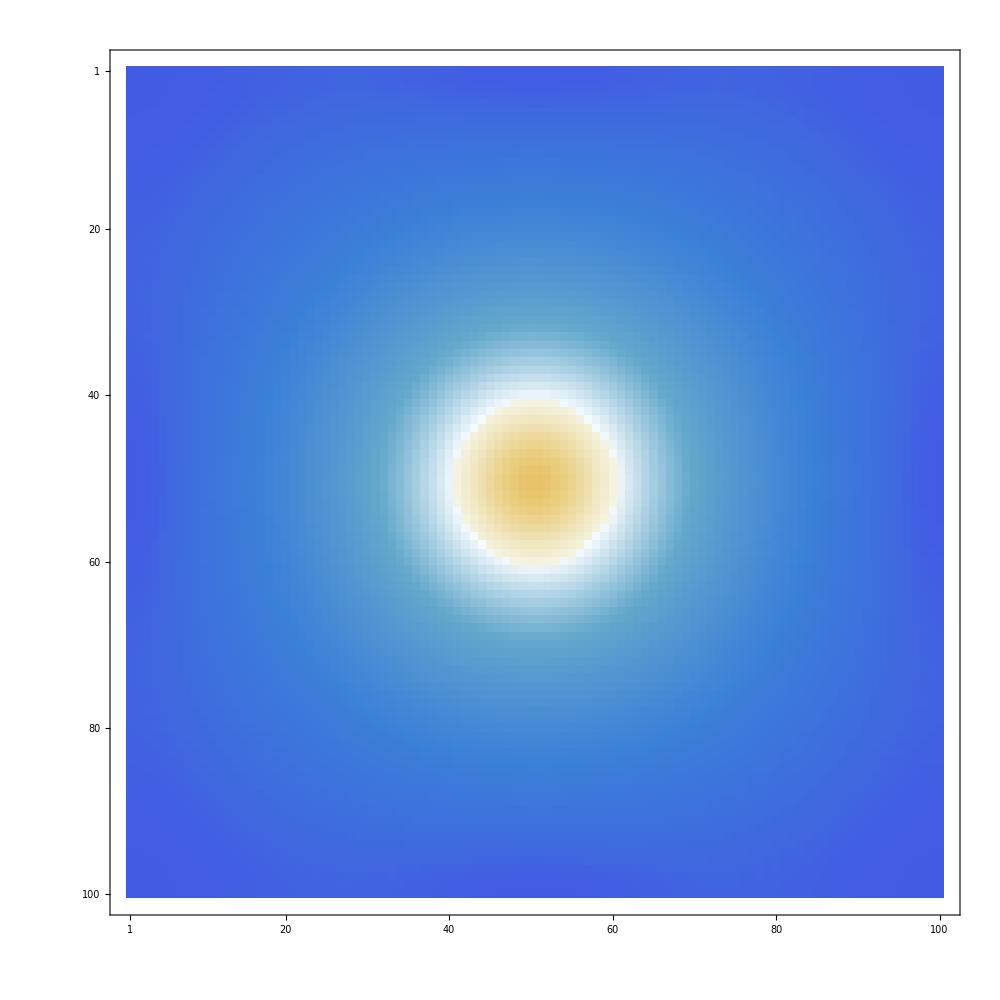

```mathematica
MatrixPlot[rawData[[1,1]][[All,All,3]]]
```

```mathematica
T = 0.09;DMI=0.02;H=-0.0014;ED="0.0";PMA="0.0";tFree = 2.0;
res=getCollapseTimes[ParentDirectory[]<>"/data/thermal-collapse-data/topological_charge_during_dynamics",T,H,DMI,ED,PMA,tFree]
p = fit2exp[cTimes,T,H]
```

{}

```mathematica
allCandT = {#,getAllCollapseTimes[Import["data/skyrmion/"<>dataType<>"*_T="<>ToString[#]<>"_H="<>ToString[H]<>"_DDI="<>ToString[ED]<>"_PMA="<>ToString[PMA]<>"*","Data"][[All,1]],tFree]}&/@Range[0.02,0.1,0.01];
```

```mathematica
processCollapseTimes[allCandT]
```

{{50.,0.00003756},{33.3333,0.000025787},{25.,0.0000225982},{20.,0.0000167792},{16.6667,0.0000168145},{14.2857,0.0000145796},{12.5,0.0000134964},{11.1111,0.0000124898},{10.,0.000012034}}

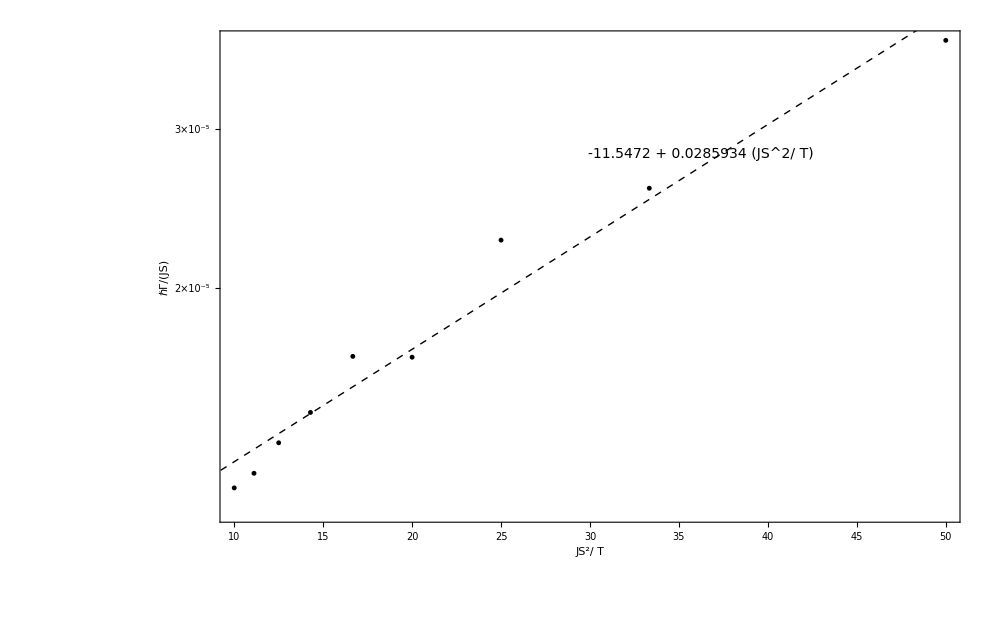

```mathematica
plotGammaVsT[allCandT]
```

Save collapse times

```mathematica
(* Since imporing thousands of topological charge lists and processing them all takes time, it is advantageous to process them once to extract the collapse time at each run, and save the results to the folder ParentDirectory[]<>"/data/processed-collapse-times" *)
```

Import and plot collapse times

```mathematica
H=-0.0014;

(* Original data was only labeled with magnetic field because we did not include PMA and DDI in those calculations. Updated data should use the more versatile fileSuffix below *)
fileNameOLD="collapse-times_H="<>ToString[H]<>".csv";
fileName="collase_times_H="<>ToString[H]<>"_DDI="<>ToString[ED]<>"_PMA="<>ToString[PMA]".csv";

collapseTimes = ToExpression@Import[ParentDirectory[]<>"/data/processed-collapse-times/"<>fileNameOLD,"CSV"];
```

```mathematica
(* 

Plot Γ as a function of 1/T *)
plotGammaVsT[collapseTimes]
```